## TRT 中用到的双线性插值算法

```mathematica
描述图像时使用格点二维索引，从零开始计数，索引可以很大且图像可以不是正方形。如 A(1023,212) 表示图 A 的第 1024 行第 213 列的格点

描述坐标时使用归一化坐标，规定左上角角落为原点 O(0,0)，数值向下为 h 正方向（第 1 分量），水平向右为 w 正方向（第 1 分量），右下角角落为 Z(1,1)。如 P(1/2,1/3) 表示坐标中一半高度、水平三等分偏左的点

原始图像相关变量用下标 1 表示，新图像相关变量用下标 2 标示。如 h1，w1，h2，w2 分别表示原图像高度、原图像宽度、新图像高度、新图像宽度
```

### 1，pyTorch，align_corners = False

```mathematica
"torch.nn.functional.interpolate(aa,size=(h,w),mode='bilinear',align_corners=False)"
```

```mathematica
将原始图像的四个角（而不是栅格的中心点）与新图像的四个角重合，以新图像左上角角落为原点建立坐标系,然后计算新图像的各栅格中心点在原图像坐标系中的坐标，并进行双线性插值
原图像上栅格[i,j]坐标：Subscript[P, i,j]=(1/(2 Subscript[h, 1])+i/Subscript[h, 1],1/(2 Subscript[w, 1])+j/Subscript[w, 1]),i=Subscript[D, 0]^(Subscript[h, 1]-1),j=Subscript[D, 0]^(Subscript[w, 1]-1)，加半格高度和宽度，从左上角偏移道栅格中心
新图像上栅格[i,j]坐标：Subscript[Q, i,j]=(1/(2 Subscript[h, 2])+i/Subscript[h, 2],1/(2 Subscript[w, 2])+j/Subscript[w, 2]),i=Subscript[D, 0]^(Subscript[h, 2]-1),j=Subscript[D, 0]^(Subscript[w, 2]-1)，形式相同，只是图像尺寸导致的归一化常数不同
求新图像上栅格 Subscript[Dst, a,b] 的值时要找到原图像上的四个栅格用于插值，Subscript[记左上角的栅格为Src, i,j] 则有：Subscript[hSrc, i,j]<Subscript[hDst, a,b]≤Subscript[hSrc, i+1,j]，Subscript[wSrc, i,j]<Subscript[wDst, a,b]≤Subscript[wSrc, i,j+1]
即：1/(2 Subscript[h, 1])+i/Subscript[h, 1]<1/(2 Subscript[h, 2])+a/Subscript[h, 2]≤1/(2 Subscript[h, 1])+(i+1)/Subscript[h, 1],1/(2 Subscript[w, 1])+j/Subscript[w, 1]<1/(2 Subscript[w, 2])+b/Subscript[w, 2]≤1/(2 Subscript[w, 1])+(j+1)/Subscript[w, 1]
记：α=Subscript[h, 1]/Subscript[h, 2](a+1/2)-1/2,β=Subscript[w, 1]/Subscript[w, 2](b+1/2)-1/2，则解可以写成：i=⌊α⌋,j=⌊β⌋
注意到原图像中两个相邻栅格中心点距离分别为：1/Subscript[h, 1],1/Subscript[w, 1]
于是插值的结果：
Subscript[V, a,b]'=((Subscript[hSrc, i+1,j]-Subscript[hDst, a,b])/(1/Subscript[h, 1]))((Subscript[wSrc, i,j+1]-Subscript[wDst, a,b])/(1/Subscript[w, 1]))Subscript[V, i,j]+((Subscript[Dst, a,b]-Subscript[hSrc, i,j])/(1/Subscript[h, 1]))((Subscript[wSrc, i,j+1]-Subscript[wDst, a,b])/(1/Subscript[w, 1]))Subscript[V, i+1,j]+((Subscript[hSrc, i+1,j]-Subscript[hDst, a,b])/(1/Subscript[h, 1]))((Subscript[wDst, a,b]-Subscript[wSrc, i,j])/(1/Subscript[w, 1]))Subscript[V, i,j+1]+((Subscript[hDst, a,b]-Subscript[hSrc, i,j])/(1/Subscript[h, 1]))((Subscript[wDst, a,b]-Subscript[wSrc, i,j])/(1/Subscript[w, 1]))Subscript[V, i+1,j+1]
	=(1-{α})(1-{β})Subscript[V, i,j]+{α}(1-{β})Subscript[V, i+1,j]+(1-{α}){β}Subscript[V, i,j+1]+{α}{β}Subscript[V, i+1,j+1]，{}表示取小数部分，{x}=x-⌊x⌋
```

### 2，pyTorch，align_corners = True，或 tensorRT，align_corners = True

```mathematica
"torch.nn.functional.interpolate(aa,size=(h,w),mode='bilinear',align_corners=True)"
```

```mathematica
将原始图像四个角栅格的中心点与新图像的四个角栅格中心点对齐，以新图像右上角角落为原点建立坐标系
原图像上栅格[i,j]坐标：Subscript[P, i,j]=(1/(2 Subscript[h, 2])+(i(Subscript[h, 2]-1))/(Subscript[h, 2](Subscript[h, 1]-1)),1/(2 Subscript[w, 2])+(j(Subscript[w, 2]-1))/(Subscript[w, 2](Subscript[w, 1]-1))),i=Subscript[D, 0]^(Subscript[h, 1]-1),j=Subscript[D, 0]^(Subscript[w, 1]-1)，半格偏移是新图像的，另外因为边长发生了缩放，多乘一个因子，可以考虑 i=0 和 i=Subscript[h, 1]-1 的情况方便理解
新图像上栅格[i,j]坐标：Subscript[Q, i,j]=(1/(2 Subscript[h, 2])+i/Subscript[h, 2],1/(2 Subscript[w, 2])+j/Subscript[w, 2]),i=Subscript[D, 0]^(Subscript[h, 2]-1),j=Subscript[D, 0]^(Subscript[w, 2]-1)，与前面相同
计算过程相同，只是把代换变成：α=(Subscript[h, 1]-1)/(Subscript[h, 2]-1)a,β=(Subscript[w, 1]-1)/(Subscript[w, 2]-1)b
注意到原图像中两个相邻栅格中心点距离分别为：(Subscript[h, 2]-1)/(Subscript[h, 2](Subscript[h, 1]-1)),(Subscript[w, 2]-1)/(Subscript[w, 2](Subscript[w, 1]-1))
可以得到一模一样的插值公式：Subscript[V, a,b]'=(1-{α})(1-{β})Subscript[V, i,j]+{α}(1-{β})Subscript[V, i+1,j]+(1-{α}){β}Subscript[V, i,j+1]+{α}{β}Subscript[V, i+1,j+1]
```

### 3，tensorRT，align_corners = False

```mathematica
"tensorrt.IResizeLayer.align_corners = False"
```

```mathematica
先将原图像和新图像分别归一化，然后将原图像左上角栅格的中心与新图像左上角栅格的中心对齐，不做进一步的缩放工作，以新图像右上角角落为原点建立坐标系
原图像上栅格[i,j]坐标：Subscript[P, i,j]=(1/(2 Subscript[h, 2])+i/Subscript[h, 1],1/(2 Subscript[w, 2])+j/Subscript[w, 1]),i=Subscript[D, 0]^(Subscript[h, 1]-1),j=Subscript[D, 0]^(Subscript[w, 1]-1)，半格偏移是新图像的，但整格距离仍是原图像的
新图像上栅格[i,j]坐标：Subscript[Q, i,j]=(1/(2 Subscript[h, 2])+i/Subscript[h, 2],1/(2 Subscript[w, 2])+j/Subscript[w, 2]),i=Subscript[D, 0]^(Subscript[h, 2]-1),j=Subscript[D, 0]^(Subscript[w, 2]-1)，与前面相同
计算过程相同，只是把代换变成：α=Subscript[h, 1]/Subscript[h, 2] a,β=Subscript[w, 1]/Subscript[w, 2] b
注意到原图像中两个相邻栅格中心点距离分别为：1/Subscript[h, 1],1/Subscript[w, 1]
可以得到一模一样的插值公式：Subscript[V, a,b]'=(1-{α})(1-{β})Subscript[V, i,j]+{α}(1-{β})Subscript[V, i+1,j]+(1-{α}){β}Subscript[V, i,j+1]+{α}{β}Subscript[V, i+1,j+1]
```

## 图示

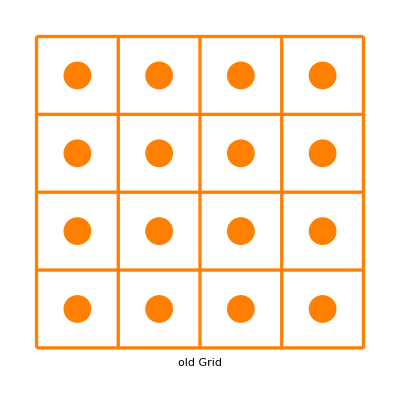

```mathematica
Graphics[{
{Thickness[0.006],RGBColor[1,0.5,0],Line[{
{{-1,1},{1,1}},{{-1,1/2},{1,1/2}},{{-1,0},{1,0}},{{-1,-1/2},{1,-1/2}},{{-1,-1},{1,-1}},
{{-1,1},{-1,-1}},{{-1/2,1},{-1/2,-1}},{{0,1},{0,-1}},{{1/2,1},{1/2,-1}},{{1,1},{1,-1}}
}]},
{PointSize[0.05],RGBColor[1,0.5,0],Point[
Flatten[Table[{i,j},{i,-3/4,3/4,1/2},{j,-3/4,3/4,1/2}],1]
]},
Text[Style["old Grid",Large],{0,-1.1}]
},AspectRatio->1,PlotRange->1.2,Axes->False,Frame->False]
```

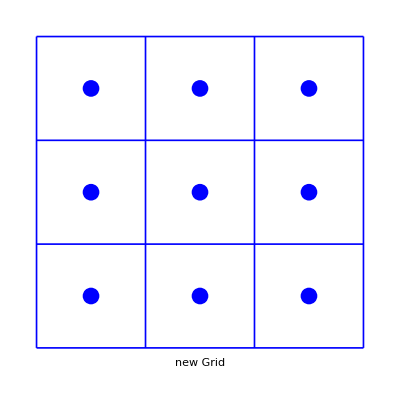

```mathematica
Graphics[{
{Thickness[0.003],RGBColor[0,0,1],Line[{
{{-1,1},{1,1}},{{-1,1/3},{1,1/3}},{{-1,-1/3},{1,-1/3}},{{-1,-1},{1,-1}},
{{-1,1},{-1,-1}},{{-1/3,1},{-1/3,-1}},{{1/3,1},{1/3,-1}},{{1,1},{1,-1}}
}]},
{PointSize[0.03],RGBColor[0,0,1],Point[Flatten[Table[{i,j},{i,-2/3,2/3,2/3},{j,-2/3,2/3,2/3}],1]]},
Text[Style["new Grid",Large],{0,-1.1}]
},AspectRatio->1,PlotRange->1.2,Axes->False,Frame->False]
```

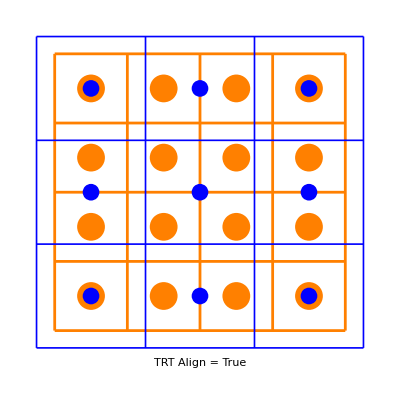

```mathematica
Graphics[{
{Thickness[0.005],RGBColor[1,0.5,0],Line[{
{{-1,1},{1,1}},{{-1,1/2},{1,1/2}},{{-1,0},{1,0}},{{-1,-1/2},{1,-1/2}},{{-1,-1},{1,-1}},
{{-1,1},{-1,-1}},{{-1/2,1},{-1/2,-1}},{{0,1},{0,-1}},{{1/2,1},{1/2,-1}},{{1,1},{1,-1}}
}*8/9]},
{PointSize[0.05],RGBColor[1,0.5,0],Point[
Flatten[Table[{i,j},{i,-3/4,3/4,1/2},{j,-3/4,3/4,1/2}],1]*8/9
]},
{Thickness[0.003],RGBColor[0,0,1],Line[{
{{-1,1},{1,1}},{{-1,1/3},{1,1/3}},{{-1,-1/3},{1,-1/3}},{{-1,-1},{1,-1}},
{{-1,1},{-1,-1}},{{-1/3,1},{-1/3,-1}},{{1/3,1},{1/3,-1}},{{1,1},{1,-1}}
}]},
{PointSize[0.03],RGBColor[0,0,1],Point[
Flatten[Table[{i,j},{i,-2/3,2/3,2/3},{j,-2/3,2/3,2/3}],1]
]},
(*{RGBColor[0,0,0],Arrow[{
{{-1/4,3/4},{0,3/4}},{{1/4,3/4},{0,3/4}},{{-3/4,1/4},{-3/4,0}},{{-3/4,-1/4},{-3/4,0}},
{{-1/4,-3/4},{0,-3/4}},{{1/4,-3/4},{0,-3/4}},{{3/4,1/4},{3/4,0}},{{3/4,-1/4},{3/4,0}},
{{-1/4,1/4},{0,0}},{{-1/4,-1/4},{0,0}},{{1/4,1/4},{0,0}},{{1/4,-1/4},{0,0}}
}*8/9]},*)
Text[Style["TRT Align = True",Large],{0,-1.1}]
},AspectRatio->1,PlotRange->1.2,Axes->False,Frame->False]
```

```mathematica
δ=1/12;
Graphics[{
{Thickness[0.005],RGBColor[1,0.5,0],Line[
Map[#+{{δ,-δ},{δ,-δ}}&,{
{{-1,1},{1,1}},{{-1,1/2},{1,1/2}},{{-1,0},{1,0}},{{-1,-1/2},{1,-1/2}},{{-1,-1},{1,-1}},
{{-1,1},{-1,-1}},{{-1/2,1},{-1/2,-1}},{{0,1},{0,-1}},{{1/2,1},{1/2,-1}},{{1,1},{1,-1}}
}]
]},
{PointSize[0.05],RGBColor[1,0.5,0],Point[
Flatten[Table[{i+δ,j-δ},{i,-3/4,3/4,1/2},{j,-3/4,3/4,1/2}],1]
]},
{Thickness[0.003],RGBColor[0,0,1],Line[{
{{-1,1},{1,1}},{{-1,1/3},{1,1/3}},{{-1,-1/3},{1,-1/3}},{{-1,-1},{1,-1}},
{{-1,1},{-1,-1}},{{-1/3,1},{-1/3,-1}},{{1/3,1},{1/3,-1}},{{1,1},{1,-1}}
}]},
{PointSize[0.03],RGBColor[0,0,1],Point[
Flatten[Table[{i,j},{i,-2/3,2/3,2/3},{j,-2/3,2/3,2/3}],1]
]},
(*{RGBColor[0,0,0],Arrow[{
{{-1/4+δ,3/4-δ},{0,2/3}},{{1/4+δ,3/4-δ},{0,2/3}},
{{1/4+δ,3/4-δ},{2/3,2/3}},{{3/4+δ,3/4-δ},{2/3,2/3}},
{{-3/4+δ,1/4-δ},{-2/3,0}},{{-3/4+δ,-1/4-δ},{-2/3,0}},
{{-3/4+δ,-1/4-δ},{-2/3,-2/3}},{{-3/4+δ,-3/4-δ},{-2/3,-2/3}},

{{-1/4+δ,1/4-δ},{0,0}},{{1/4+δ,1/4-δ},{0,0}},
{{-1/4+δ,-1/4-δ},{0,0}},{{1/4+δ,-1/4-δ},{0,0}},

{{-1/4+δ,-3/4-δ},{0,-2/3}},{{1/4+δ,-3/4-δ},{0,-2/3}},
{{-1/4+δ,-1/4-δ},{0,-2/3}},{{1/4+δ,-1/4-δ},{0,-2/3}},

{{1/4+δ,1/4-δ},{2/3,0}},{{3/4+δ,1/4-δ},{2/3,0}},
{{1/4+δ,-1/4-δ},{2/3,0}},{{3/4+δ,-1/4-δ},{2/3,0}},

{{1/4+δ,-1/4-δ},{2/3,-2/3}},{{3/4+δ,-1/4-δ},{2/3,-2/3}},
{{1/4+δ,-3/4-δ},{2/3,-2/3}},{{3/4+δ,-3/4-δ},{2/3,-2/3}}
}]},*)
Text[Style["TRT Align = False",Large],{0,-1.2}]
},AspectRatio->1,PlotRange->1.3,Axes->False,Frame->False]
```

-Graphics-

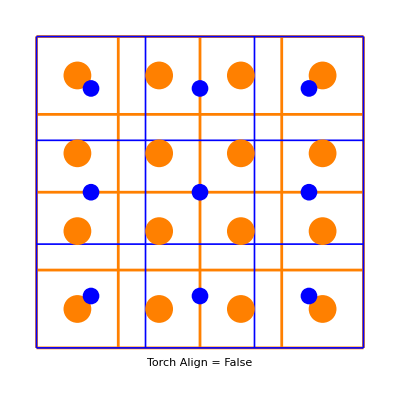

```mathematica
Graphics[{
{Thickness[0.005],RGBColor[1,0.5,0],Line[{
{{-1,1},{1,1}},{{-1,1/2},{1,1/2}},{{-1,0},{1,0}},{{-1,-1/2},{1,-1/2}},{{-1,-1},{1,-1}},
{{-1,1},{-1,-1}},{{-1/2,1},{-1/2,-1}},{{0,1},{0,-1}},{{1/2,1},{1/2,-1}},{{1,1},{1,-1}}
}]},
{Thickness[0.003],RGBColor[0,0,1],Line[{
{{-1,1},{1,1}},{{-1,1/3},{1,1/3}},{{-1,-1/3},{1,-1/3}},{{-1,-1},{1,-1}},
{{-1,1},{-1,-1}},{{-1/3,1},{-1/3,-1}},{{1/3,1},{1/3,-1}},{{1,1},{1,-1}}
}]},
{PointSize[0.05],RGBColor[1,0.5,0],Point[
Flatten[Table[{i,j},{i,-3/4,3/4,1/2},{j,-3/4,3/4,1/2}],1]
]},
{PointSize[0.03],RGBColor[0,0,1],Point[Flatten[Table[{i,j},{i,-2/3,2/3,2/3},{j,-2/3,2/3,2/3}],1]]},
(*{RGBColor[0,0,0],Arrow[{
{{-3/4,3/4},{-2/3,2/3}},{{-1/4,3/4},{-2/3,2/3}},
{{-3/4,1/4},{-2/3,2/3}},{{-1/4,1/4},{-2/3,2/3}},
{{-1/4,3/4},{0,2/3}},{{1/4,3/4},{0,2/3}},
{{-1/4,1/4},{0,2/3}},{{1/4,1/4},{0,2/3}},
{{1/4,1/4},{2/3,2/3}},{{3/4,1/4},{2/3,2/3}},
{{1/4,3/4},{2/3,2/3}},{{3/4,3/4},{2/3,2/3}},

{{-3/4,1/4},{-2/3,0}},{{-1/4,1/4},{-2/3,0}},
{{-3/4,-1/4},{-2/3,0}},{{-1/4,-1/4},{-2/3,0}},
{{-1/4,1/4},{0,0}},{{1/4,1/4},{0,0}},
{{-1/4,-1/4},{0,0}},{{1/4,-1/4},{0,0}},
{{1/4,1/4},{2/3,0}},{{3/4,1/4},{2/3,0}},
{{1/4,-1/4},{2/3,0}},{{3/4,-1/4},{2/3,0}},

{{-3/4,-1/4},{-2/3,-2/3}},{{-1/4,-1/4},{-2/3,-2/3}},
{{-3/4,-3/4},{-2/3,-2/3}},{{-1/4,-3/4},{-2/3,-2/3}},
{{-1/4,-3/4},{0,-2/3}},{{1/4,-3/4},{0,-2/3}},
{{-1/4,-1/4},{0,-2/3}},{{1/4,-1/4},{0,-2/3}},
{{1/4,-1/4},{2/3,-2/3}},{{3/4,-1/4},{2/3,-2/3}},
{{1/4,-3/4},{2/3,-2/3}},{{3/4,-3/4},{2/3,-2/3}}
}]},*)
Text[Style["Torch Align = False",Large],{0,-1.1}]
},AspectRatio->1,PlotRange->1.2,Axes->False,Frame->False]
```